### Mean and variance: ⟨y⟩ = ∫y × p(y)ⅆy σ^2(y) = ⟨(δy)^2⟩= ∫(y-⟨y⟩)^2 × p(y)ⅆy ; δy = y-⟨y⟩ The square root of the variance is known as the standard deviation. It also comes under the name of root-mean-squared deviation σ(y) = Δy_rms = √(σ^2(y))= √⟨(δy)^2⟩= √⟨(y-⟨y⟩)^2⟩ Note that standard deviation itself is not a type of averaging and it cannot be calculated directly by integrating over the probability density function (like mean and variance introduced above).

## PHY-473: Discrete Poisson Process

### Poisson Distribution Function

Poisson distribution gives the probability of an event to occur k times during the time t given the rate of occurrence equal to r. One can define the average number of events during time t: μ = t × k
			
							P(n) =μ^n/(n!) e^-μ

(ⅇ^-μ μ^k)/(k!)

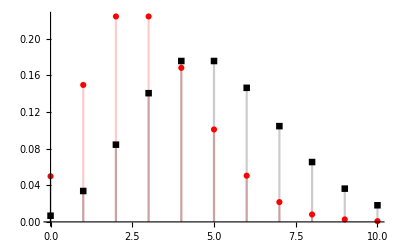

```mathematica
Clear[μ,variance,k]
poisson[k_,μ_]=Exp[-μ]*μ^k/k!
DiscretePlot[{poisson[k,3],poisson[k,5]},{k,0,10},PlotStyle->{Red,Black},PlotMarkers->Automatic]
```

### Mean

```mathematica
mean[μ_]:=Sum[k*poisson[k,μ],{k,0,∞}]
Print[" mean at μ=10, ",mean[10]]
```

mean at μ=10, 10

### Variance

```mathematica
variance[μ_]:=Sum[k^2*poisson[k,μ],{k,0,∞}]-Sum[k*poisson[k,μ],{k,0,∞}]^2
Print[" variance at μ=10, ",variance[10]]
```

variance at μ=10, 10

### Customers in the shop example

Customers come to the shop with the frequency of 100 per 8 hours. Evaluate the probability of only 2 customers arriving between 1 pm and 3 pm

```mathematica
Print[" Expected average ",μ=100/8*2]
PDF[PoissonDistribution[25],x]/.x->2
N[%]
```

Expected average 25

625/(2 ⅇ^25)

4.33998×10^-9

### Collisions example

The number of collisions of molecules with the wall is 10^12/s. Calculate the probability of 20 collisions in 30 ps

```mathematica
μ=30;
Print[" probability of 20 collisions = ",poisson[20,30]//N]
```

probability of 20 collisions = 0.0134112

## Connection to the Gaussian distribution

The Gaussian distribution defined here maintains the properties of the Poisson distribution
			<x> = σ^2 = μ

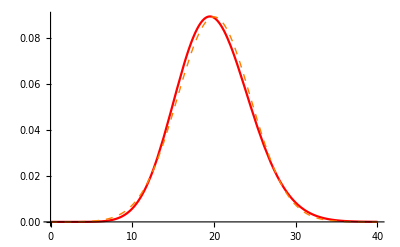

```mathematica
gp[x_,μ_]:=Exp[-(x-μ)^2/(2μ)]/Sqrt[2*π*μ]
Plot[{poisson[k,20],gp[k,20]},{k,0,40},PlotStyle->{{Red},{Orange,Dashed,Thick}}]
```